```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"img"}]];
voltsNeeded[h1_,h2_,d1_,B_,E1_]:=h1*h2*B*Sqrt[2*E1*1.6*^-19]/d1/Sqrt[9.11*^-31];
plateLengthNeeded[h1_,h2_,V_,B_,E1_]:=h1*h2*B*Sqrt[2*E1*1.6*^-19]/V/Sqrt[9.11*^-31];
```

```mathematica
h1=.009; (* separation between the plates (m)*)
h2= .011 ;(* desired displacement of electron (m) *)
d1=.07112;(*Length of deflecting plates (m) *)
B=.02 ;(* magnetic field, (Tesla) *)
E1=e ;(*electron energy (eV) *)
```

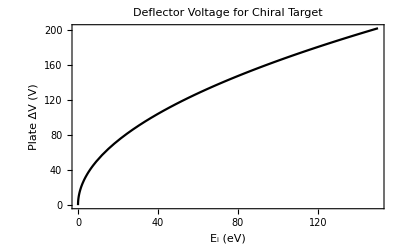

```mathematica
defPlot=Plot[voltsNeeded[h1,h2,d1,B,e],{e,0,150},FrameLabel->{"E_i (eV)","Plate ΔV (V)"},PlotStyle->Black,PlotLabel->"Deflector Voltage for Chiral Target",ImageSize->{UpTo[3*72],UpTo[72*2]},LabelStyle->10]
```

```mathematica
Export["upTo150eVDeflectorVoltages.png",defPlot,ImageResolution->200]
```

upTo150eVDeflectorVoltages.png

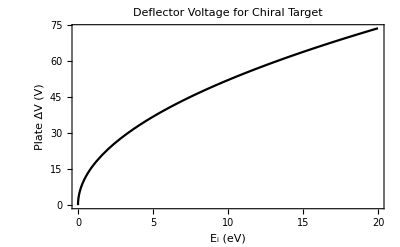

```mathematica
defPlot=Plot[voltsNeeded[h1,h2,d1,B,e],{e,0,20},FrameLabel->{"E_i (eV)","Plate ΔV (V)"},PlotStyle->Black,PlotLabel->"Deflector Voltage for Chiral Target",ImageSize->{UpTo[3*72],UpTo[72*2]},LabelStyle->10]
```

```mathematica
Export["upTo5eVDeflectorVoltages.png",defPlot,ImageResolution->200]
```

upTo5eVDeflectorVoltages.png

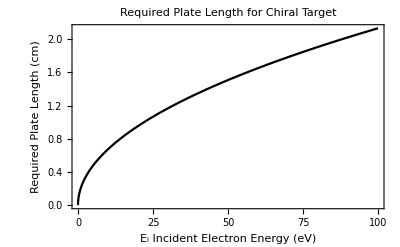

```mathematica
Plot[plateLengthNeeded[.01,.018,1000,.02,e]*100,{e,0,100},FrameLabel->{"E_i Incident Electron Energy (eV)","Required\n Plate Length (cm)"},PlotStyle->Black,PlotLabel->"Required Plate Length for Chiral Target"]
```

```mathematica
h1=.009; (* separation between the plates (m)*)
h2= .009+.018/2 (* desired displacement of electron (m) *)
d1=.07112;(*Length of deflecting plates (m) *)
B=.0150 ;(* magnetic field, (Tesla) *)
E1=e ;(*electron energy (eV) *)
```

0.018

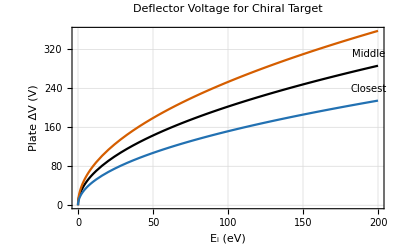

```mathematica
defPlot=Plot[{voltsNeeded[h1,h2,d1,B,e],voltsNeeded[h1,h2+.009/2,d1,B,e],voltsNeeded[h1,h2-.009/2,d1,B,e]},{e,0,200},FrameLabel->{"E_i (eV)","Plate ΔV (V)"},PlotLabel->"Deflector Voltage for Chiral Target",ImageSize->{UpTo[6*72],UpTo[72*4]},LabelStyle->10, GridLines->Automatic,PlotLabels->Placed[{"Middle","Furthest","Closest"},Above]]
```